```mathematica
Log1[x_]:= If[x==0,0,Log2[Abs[x]]];
VEntropy[x_]:= -(x Log1[x] + (1-x)Log1[1-x]);
Prob[a_,b_,x_,y_]:= 1-(x^2y^2)/(a^2y^2+b^2x^2);
Cost[a_,b_,x_,y_] := VEntropy[x^2] + Prob[a,b,x,y];
Newa[a_,b_,x_,y_]:=((x^2-y^2)a*b)/(Sqrt[x^4b^2+y^4a^2]);
Cost2[a_,b_,x_,y_,x1_,y1_]:=  VEntropy[x^2] + Prob[a,b,x,y](Cost[Newa[a,b,x,y],Sqrt[1-Newa[a,b,x,y]^2],x1,y1])
Anlist = Anlist2={}
For[ar=0, ar<1,ar=ar+0.01,Anlist = Append[Anlist,{VEntropy[ar^2],NMinimize[{Cost2[ar,Sqrt[1-ar^2],x,Sqrt[1-x^2],x1,Sqrt[1-x1^2]],0≤x≤1&&0≤x1≤1},{x,x1},Method->"DifferentialEvolution"][[1]]}]]
For[ar=0, ar<1,ar=ar+0.01,Anlist2 = Append[Anlist2,{VEntropy[ar^2],NMinimize[{Cost[ar,Sqrt[1-ar^2],x,Sqrt[1-x^2]],0≤x≤1},{x},Method->"DifferentialEvolution"][[1]]}]]
```

{}

```mathematica
Clear[Cost3]
Cost3[a_,b_,x_,y_,x1_,y1_,x2_,y2_]:=VEntropy[x^2] + Prob[a,b,x,y](Cost2[Newa[a,b,x,y],Sqrt[1-Newa[a,b,x,y]^2],x1,y1,x2,y2])
Anlist3={}
For[ar=0, ar<1,ar=ar+0.01,Anlist3 = Append[Anlist3,{VEntropy[ar^2],NMinimize[{Cost3[ar,Sqrt[1-ar^2],x,Sqrt[1-x^2],x1,Sqrt[1-x1^2],x2,Sqrt[1-x2^2]],0≤x≤1&&0≤x1≤1&&0≤x2≤1},{x,x1,x2},Method->"DifferentialEvolution"][[1]]}]]
```

{}

```mathematica
Anlist3-Anlist
```

{{0,0.},{0.,-0.00134639},{0.,2.6229×10^-15},{0.,2.52576×10^-15},{0.,-1.94289×10^-16},{0.,-4.16334×10^-16},{0.,2.77556×10^-16},{0.,-2.72005×10^-15},{0.,1.60982×10^-15},{0.,-3.27516×10^-15},{0.,-2.38698×10^-15},{0.,-3.66374×10^-15},{0.,-3.21965×10^-15},{0.,-2.9976×10^-15},{0.,3.33067×10^-16},{0.,-4.44089×10^-16},{0.,-2.22045×10^-16},{0.,-2.22045×10^-16},{0.,6.66134×10^-16},{0.,-4.44089×10^-16},{0.,4.44089×10^-16},{0.,2.22045×10^-16},{0.,-4.44089×10^-16},{0.,-1.11022×10^-16},{0.,0.},{0.,6.66134×10^-16},{0.,6.66134×10^-16},{0.,5.55112×10^-16},{0.,1.11022×10^-16},{0.,-3.66374×10^-15},{0.,-6.66134×10^-16},{0.,1.11022×10^-16},{0.,-4.44089×10^-16},{0.,1.11022×10^-16},{0.,-1.11022×10^-16},{0.,-6.66134×10^-16},{0.,2.22045×10^-16},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,2.22045×10^-16},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,2.22045×10^-16},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,4.44089×10^-16},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,-8.32667×10^-15},{0.,1.03251×10^-14},{0.,-3.55271×10^-15},{0.,6.32827×10^-15},{0.,-2.22045×10^-16},{0.,4.44089×10^-16}}

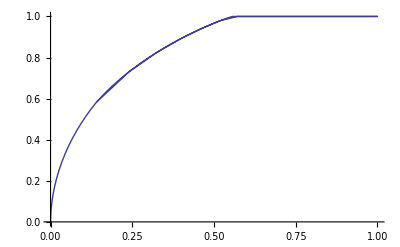

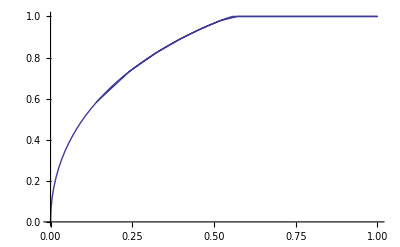

```mathematica
p1=ListLinePlot[Anlist]
p2=ListLinePlot[Anlist2]
Show[p1,p2]
```

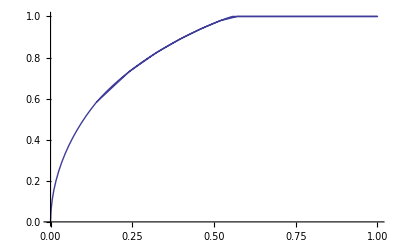

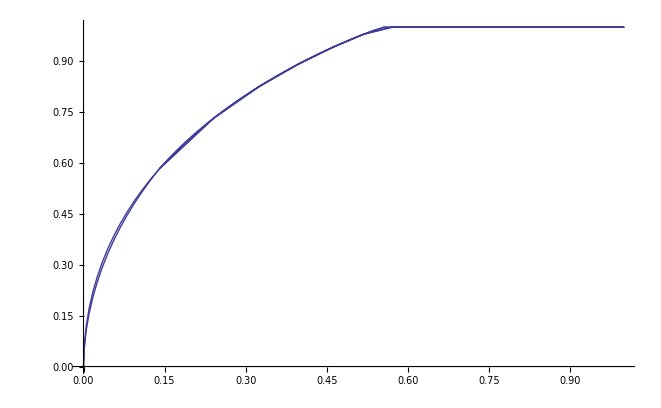

```mathematica
p3= ListLinePlot[Anlist3]
Show[p2,p3]
```